```mathematica
Quit[]
```

```mathematica
Get["Alex`"];
```

Assured Flow Solutions' Alex v2019.8.0

### Some data setup

```mathematica
ds=Table[<|
"S"->RandomChoice[{"Male","Missing","Female"}],
"Age"->RandomInteger[{10,70}],
"Income"->RandomReal[{50000,150000}],
"Weight"->RandomReal[{100,250}]
|>,{1000}];
```

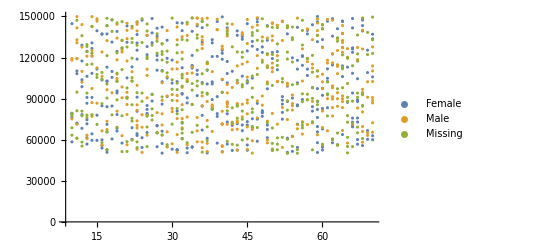

```mathematica
ds//GroupBy[#S&->({#Age,#Income}&)]//ListPlot
```

```mathematica
mpg=Import[FileNameJoin[{NotebookDirectory[],"mpg.csv"}]];
mpg=mpg//Map[AssociationThread[mpg[[1]]->#]&,Rest[#]]&;
```

```mathematica
mpg[[1]]
```

<|manufacturer→audi,model→a4,displ→1.8,year→1999,cyl→4,trans→auto(l5),drv→f,cty→18,hwy→29,fl→p,class→compact|>

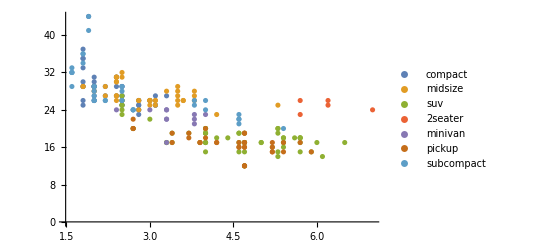

```mathematica
mpg//GroupBy[#class&->({#displ,#hwy}&)]//ListPlot
```

#### Initial testing and messing around

Symbols

```mathematica
ggPlot;
geomPoint;
geomLine;
aes;
```

Function signature

```mathematica
Remove[geomPoint,geomLine]
```

```mathematica
geom["Point",{x_,y_},aes[__]..];
geom["Line",{x_,y_},aes[__]..];
```

```mathematica
aes["Color",key_];
aes["MarkerSize",key_];
```

```mathematica
geom;
aes;
```

```mathematica
resolveGeom[dataset_,"Point",g_]:=Module[{xKey,yKey,colorKey,markersizeKey,colorsDiscreteQ,markerSizeDiscreteQ,groupKey,output,colorFunc,markerSizeFunc},
(*Data keys*)
{xKey,yKey}=Cases[{g},geom["Point",{x_,y_},___]:>{x,y},Infinity,1][[1]];
(*Aesthetics*)
colorKey=Check[Cases[g,aes["Color",key_]:>key,Infinity,1][[1]],{}]//Quiet;
markersizeKey=Check[Cases[g,aes["MarkerSize",key_]:>key,Infinity,1][[1]],{}]//Quiet;
(*Determine colors*)
colorFunc=Function[x,Black];
If[!MatchQ[colorKey,{}],
colorsDiscreteQ=If[MatchQ[dataset[[All,colorKey]],{_?NumericQ..}],False,True];
If[colorsDiscreteQ,
colorFunc=Sort@DeleteDuplicates[dataset[[All,colorKey]]]//AssociationThread[#->ggplotColorsFunc[Length[#]]]&,
colorFunc=Function[x,Red](*todo*)
];
];
(*Determine marker sizes*)
markerSizeFunc=Function[x,Small];
If[!MatchQ[markersizeKey,{}],
markerSizeDiscreteQ=If[MatchQ[dataset[[All,markersizeKey]],{_?NumericQ..}],False,True];
If[markerSizeDiscreteQ,
markerSizeFunc=Sort@DeleteDuplicates[dataset[[All,markersizeKey]]]//AssociationThread[#->ggplotColorsFunc[Length[#]]]&,
markerSizeFunc=Function[x,Red](*todo*)
];
];
(*Create data*)
output=Switch[{colorKey,markersizeKey},
{_?StringQ,{}},dataset//GroupBy[#[colorKey]&->({colorFunc[#[colorKey]],PointSize[Small],Point[{#[xKey],#[yKey]}]}&)],
{{},_?StringQ},dataset//GroupBy[#[markersizeKey]&->({Black,markerSizeFunc[#[markersizeKey]],Point[{#[xKey],#[yKey]}]}&)],
{_?StringQ..},dataset//GroupBy[#[{colorKey,markersizeKey}]&->({colorFunc[#[colorKey]],markerSizeFunc[#[markersizeKey]],Point[{#[xKey],#[yKey]}]}&)]
];
output
]
```

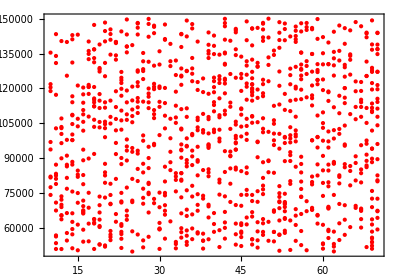

```mathematica
resolveGeom[ds,"Point",geom["Point",{"Age","Income"},aes["MarkerSize","Weight"]]]//Values//Graphics
```

```mathematica
geom["Point",{"Age","Income"},aes["MarkerSize","Weight"]]
```

```mathematica
ggPlot[dataset_,geoms:(geom[__]|{geom[__]..}),opts:OptionsPattern[]]:=Module[{primitiaves,plot},
primitiaves=Values[resolveGeom[dataset,"Point",#]]&/@Cases[geoms,geom[__],{0,Infinity}];
primitiaves//Graphics
];
```

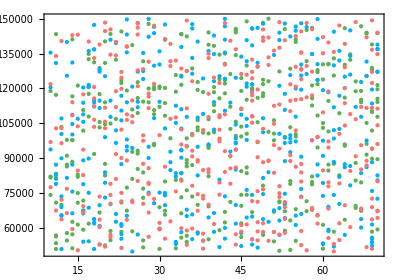

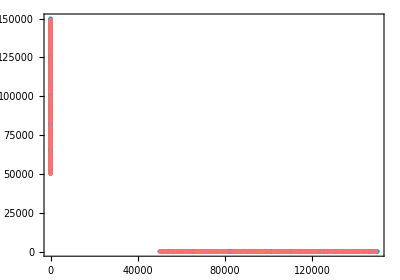

```mathematica
ggPlot[ds,geom["Point",{"Age","Income"},aes["Color","S"]]]
ggPlot[ds,{
geom["Point",{"Age","Income"},aes["Color","S"]],
geom["Point",{"Income","Age"},aes["Color","S"]]
}]
```

### Point Aesthetics (actual start of something)

• x, y (required)
• color
• size
• alpha (opacity)
• shape
• etc. (look online for more https://ggplot2.tidyverse.org/reference/geom_point.html)

Need some abstract way of creating the aesthetic desired based on the data and the selected key

```mathematica
Get["Alex`"];
```

Assured Flow Solutions' Alex v2019.8.0

#### Initial work

Default functions

```mathematica
(*colorFunc=Function[Black];*)
sizeFunc=Function[10];
alphaFunc=Function[Opacity[1]];
shapeFunc=Function["●"];
```

```mathematica
isDiscreteDataQ[data_]:=If[MatchQ[DeleteDuplicates[data],{_?StringQ..}],True,False];
getDiscreteKeys[data_]:=Sort[DeleteDuplicates[data]];
getContinuousRange[data_]:=MinMax[data];
```

```mathematica
ggplotColorsFunc[2]
```

{LCHColor[0.65, 0.6, Rational[1, 13]],LCHColor[0.65, 0.6, Rational[7, 13]]}

```mathematica
determineColorFunc[dataset_,key_]:=Module[{data,colorFunc,discreteDataQ,keys},
data=dataset[[All,key]];
colorFunc=Function[Black];
discreteDataQ=isDiscreteDataQ[data];
If[discreteDataQ,
keys=getDiscreteKeys[data];
colorFunc=AssociationThread[keys->ggplotColorsFunc[Length[keys]]];
];
If[!discreteDataQ,
colorFunc=Function[x,ColorData[1][Rescale[x,getContinuousRange[data]]]]
];
colorFunc
];
determineColorFunc[dataset_,Null]:=Function[Black];
```

```mathematica
Options[geomPoint]={"color"->Null,"size"->Null,"alpha"->Null,"shape"->Null};
geomPoint[dataset_,"x"->xKey_,"y"->yKey_,optionalAesthetics:OptionsPattern[]]:=Module[{colorFunc,output},
(*Gather keys that are needed (should be smart enough to recognize a key in the dataset)*)
(*For each key neseccary, get functions to be used to specify the aesthetic*)
colorFunc=determineColorFunc[dataset,OptionValue["color"]];
sizeFunc=sizeFunc(*determineSizeFunc[]*);
alphaFunc=alphaFunc(*determineAlphaFunc[]*);
shapeFunc=shapeFunc(*determineShapeFunc[]*);

(*Grab the point data and for each Point apply the correct aesthetic*)
output=dataset//Map[{
colorFunc[#[OptionValue["color"]]],
alphaFunc[#[OptionValue["alpha"]]],
Inset[Style[shapeFunc[#[OptionValue["shape"]]],sizeFunc[#[OptionValue["size"]]]],{#[xKey],#[yKey]}]
}&];
(*Group the data by similar aesthetics and then just apply to the first one so we reduce the memory size of the output (since graphics will apply the same forms to following expressions)*)
output=output//GroupBy[Most->Last]//Normal//ReplaceAll[Rule->List]//Flatten;
output
];
```

#### Testing (IntelliJ code)

```mathematica
mpg=Import[FileNameJoin[{NotebookDirectory[],"mpg.csv"}]];
mpg=mpg//Map[AssociationThread[mpg[[1]]->#]&,Rest[#]]&;
```

```mathematica
Get["/Users/andrewyule/Dropbox (Personal)/AFS/Source Code/ggplot/ggplot/ggplot.m"]
```

```mathematica
mpg[[1]]
```

<|manufacturer→audi,model→a4,displ→1.8,year→1999,cyl→4,trans→auto(l5),drv→f,cty→18,hwy→29,fl→p,class→compact|>

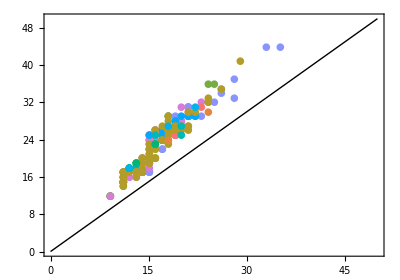

```mathematica
ggPlot[mpg,geomPoint["x"->"cty","y"->"hwy","color"->"trans"],Epilog->Line[{{0,0},{50,50}}]]
```

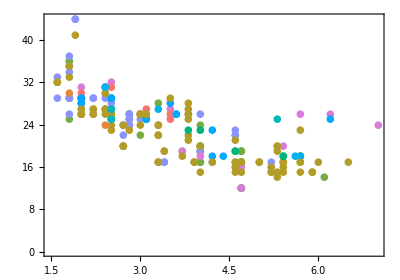

```mathematica
ggPlot[mpg,geomPoint["x"->"displ","y"->"hwy","color"->"trans"]]
```

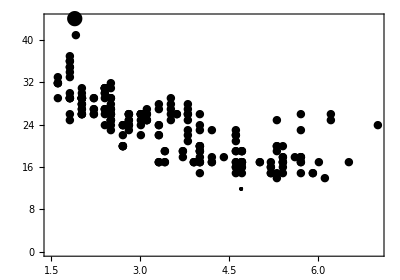

```mathematica
ggPlot[mpg,geomPoint["x"->"displ","y"->"hwy","size"->"cty"]]
```

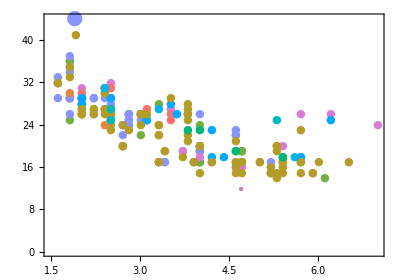

```mathematica
ggPlot[mpg,geomPoint["x"->"displ","y"->"hwy","color"->"trans","size"->"cty"]]
```

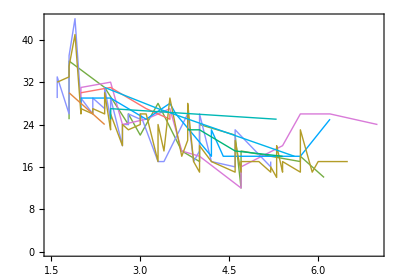

```mathematica
ggPlot[mpg,geomLine["x"->"displ","y"->"hwy","color"->"trans"]]
```

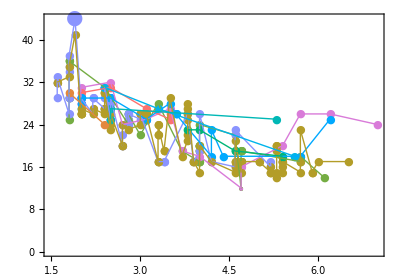

```mathematica
ggPlot[mpg,{
geomPoint["x"->"displ","y"->"hwy","color"->"trans","size"->"cty"],
geomLine["x"->"displ","y"->"hwy","color"->"trans"]
}]
```

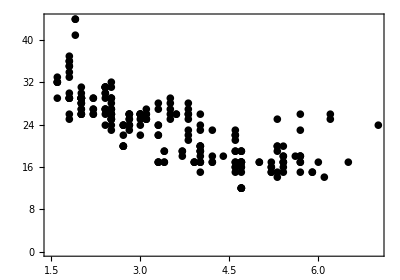

```mathematica
ggPlot[mpg,{
geomPoint["x"->"displ","y"->"hwy"]
}]
```

```mathematica
Get["/Users/andrewyule/Dropbox (Personal)/AFS/Source Code/ggplot/ggplot/ggplot.m"]
```

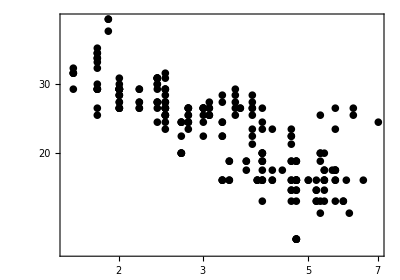

```mathematica
ggPlot[mpg,{
geomPoint["x"->"displ","y"->"hwy"]
},ScalingFunctions->{"Log","Log"}]
```

```mathematica
Reciprocal
```